## 问题

```mathematica
r1=2.25
r2=10.1258
```

```mathematica
f[α_,β_]:=BesselJ[1,r1 α]+β BesselY[1,r1 α]
F[α_,β_]:=BesselJ[0,r2 α]+β BesselY[0,r2 α]
solutions=Solve[{f[α,β]==0,F[α,β]==0},{α,β}]
Ai=α/.solutions
Bi=β/.solutions
h[Xi_,Yi_]:=((2 ∫_2.25^10.1258 r (BesselJ[0,Xi r]+Yi BesselY[0,Xi r]) 30 Log[10.1258/2.25]ⅆr) (BesselJ[0,2.25 Xi]+Yi BesselY[0,2.25 Xi]) ⅇ^(-(Xi^2 t 8)/10^8))/(10.1258^2 (BesselJ[1,10.1258 Xi]+Yi BesselY[1,10.1258 Xi])^2-2.25^2 (BesselJ[0,2.25 Xi]+Yi BesselY[0,2.25 Xi])^2)
g[Ai_,Bi_]:=∑_(n=1)^Length[Ai] h[Ai[n],Bi[n]]
result=g[Ai,Bi]
```

{}

α

β

0

## 解法

不要直接代入数值，方便解析变换

```mathematica
f[α_,β_]:=BesselJ[1,r1 α]+β BesselY[1,r1 α]
F[α_,β_]:=BesselJ[0,r2 α]+β BesselY[0,r2 α]
```

```mathematica
$Assumptions=r2>r1>0&&α>0;
values={r1->2.25,r2->10.1258};
```

看似二元，实则一元方程。β 线性，直接消掉。

```mathematica
eqn=Eliminate[{f[α,β]==0,F[α,β]==0},β]
LHS=SubtractSides[eqn][[1]]
```

BesselJ[1,r1 α] BesselY[0,r2 α]-BesselJ[0,r2 α] BesselY[1,r1 α]==0

BesselJ[1,r1 α] BesselY[0,r2 α]-BesselJ[0,r2 α] BesselY[1,r1 α]

画图找零点：显然  α 较大时像是有周期性

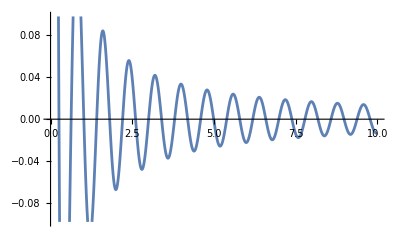

```mathematica
Plot[LHS/.values,{α,0,10}]
```

做渐进展开，取第一阶：
（计算时间稍长, ~15s）
化简，直接得到一个三角函数。所有的根一目了然

```mathematica
Asymptotic[LHS,α->∞]
asympLHS=%//FullSimplify
```

-((-1)^(3/4) ⅇ^(-ⅈ r2 α) √(r1 r2) Cos[π/4+r1 α])/(π r1 r2 α)+((-1)^(1/4) ⅇ^(ⅈ r2 α) √(r1 r2) Cos[π/4+r1 α])/(π r1 r2 α)+((-1)^(1/4) ⅇ^(-ⅈ r1 α) √(r1 r2) Cos[π/4-r2 α])/(π r1 r2 α)-((-1)^(3/4) ⅇ^(ⅈ r1 α) √(r1 r2) Cos[π/4-r2 α])/(π r1 r2 α)

(2 Cos[(r1-r2) α])/(π √(r1 r2) α)

Cos 的根有通式，则可以直接代入求和了。不妨在小 α 范围内数值解，大 α 则代入通式，则可算任意项。

画图，可以看出对于大 α 近似程度很好

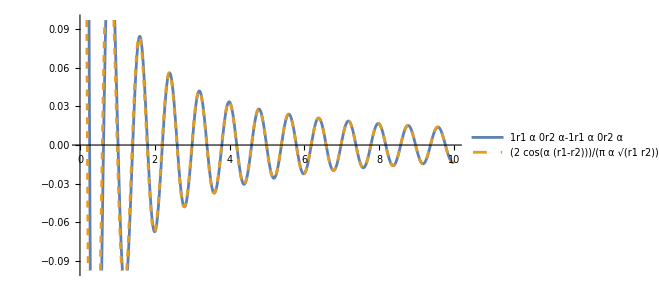

```mathematica
Plot[{LHS,asympLHS}/.values//Evaluate,{α,0,10},PlotLegends->{LHS,asympLHS},PlotStyle->{Automatic,Dashed}]
```

验证：数值求根

```mathematica
NSolveValues[{eqn,0<α<100}/.values,α];
NSolveValues[{asympLHS,0<α<100}/.values,α];
%-%%
```

{-0.0585839,-0.0316556,-0.0209917,-0.0155467,-0.0122974,-0.0101538,-0.00863877,-0.00751335,-0.00664534,-0.00595596,-0.00539548,-0.00493097,-0.00453982,-0.00420597,-0.00391772,-0.00366635,-0.00344522,-0.0032492,-0.00307425,-0.00291714,-0.00277529,-0.00264657,-0.00252925,-0.00242188,-0.00232325,-0.00223233,-0.00214824,-0.00207026,-0.00199774,-0.00193012,-0.00186693,-0.00180774,-0.00175219,-0.00169994,-0.00165072,-0.00160427,-0.00156036,-0.00151879,-0.00147938,-0.00144196,-0.00140638,-0.00137252,-0.00134025,-0.00130946,-0.00128005,-0.00125194,-0.00122503,-0.00119926,-0.00117454,-0.00115083,-0.00112805,-0.00110616,-0.0010851,-0.00106483,-0.0010453,-0.00102647,-0.00100831,-0.000990781,-0.000973851,-0.000957489,-0.000941669,-0.000926362,-0.000911546,-0.000897195,-0.00088329,-0.000869808,-0.000856732,-0.000844044,-0.000831725,-0.000819761,-0.000808137,-0.000796837,-0.000785849,-0.00077516,-0.000764757,-0.00075463,-0.000744768,-0.00073516,-0.000725797,-0.000716669,-0.000707769,-0.000699086,-0.000690614,-0.000682345,-0.000674271,-0.000666386,-0.000658684,-0.000651157,-0.000643801,-0.000636609,-0.000629575,-0.000622696,-0.000615965,-0.000609378,-0.000602931,-0.000596618,-0.000590436,-0.000584381,-0.000578449,-0.000572637,-0.000566939,-0.000561355,-0.000555879,-0.000550508,-0.000545241,-0.000540074,-0.000535003,-0.000530027,-0.000525142,-0.000520347,-0.000515638,-0.000511014,-0.000506473,-0.000502011,-0.000497627,-0.000493319,-0.000489085,-0.000484923,-0.000480831,-0.000476807,-0.000472851,-0.000468959,-0.000465132,-0.000461366,-0.00045766,-0.000454014,-0.000450425,-0.000446893,-0.000443415,-0.000439991,-0.00043662,-0.0004333,-0.00043003,-0.000426809,-0.000423636,-0.00042051,-0.000417429,-0.000414394,-0.000411402,-0.000408453,-0.000405546,-0.00040268,-0.000399854,-0.000397068,-0.000394321,-0.000391611,-0.000388938,-0.000386301,-0.0003837,-0.000381133,-0.000378601,-0.000376102,-0.000373636,-0.000371202,-0.0003688,-0.000366428,-0.000364087,-0.000361775,-0.000359493,-0.000357239,-0.000355013,-0.000352815,-0.000350644,-0.0003485,-0.000346381,-0.000344288,-0.000342221,-0.000340178,-0.000338159,-0.000336164,-0.000334192,-0.000332244,-0.000330318,-0.000328414,-0.000326532,-0.000324672,-0.000322832,-0.000321014,-0.000319215,-0.000317437,-0.000315678,-0.000313939,-0.000312219,-0.000310518,-0.000308835,-0.00030717,-0.000305523,-0.000303894,-0.000302281,-0.000300686,-0.000299108,-0.000297546,-0.000296,-0.000294471,-0.000292957,-0.000291458,-0.000289975,-0.000288507,-0.000287054,-0.000285615,-0.00028419,-0.00028278,-0.000281384,-0.000280001,-0.000278632,-0.000277276,-0.000275933,-0.000274604,-0.000273287,-0.000271982,-0.00027069,-0.00026941,-0.000268142,-0.000266887,-0.000265642,-0.00026441,-0.000263188,-0.000261978,-0.000260779,-0.000259591,-0.000258414,-0.000257248,-0.000256091,-0.000254946,-0.00025381,-0.000252685,-0.000251569,-0.000250463,-0.000249367,-0.000248281,-0.000247203,-0.000246136,-0.000245077,-0.000244027,-0.000242987,-0.000241955,-0.000240932,-0.000239918,-0.000238912,-0.000237914,-0.000236925,-0.000235944,-0.000234971,-0.000234006,-0.000233049,-0.0002321,-0.000231158,-0.000230224,-0.000229298,-0.000228379,-0.000227467}